```mathematica
(*Physical constants*)
mhe= Entity["Element", "Helium"][EntityProperty["Element", "AtomicMass"]]; (*mass of helium*)
e=Entity["Particle", "Electron"][EntityProperty["Particle", "Charge"]];
c=Quantity[None, "SpeedOfLight"];
ϵ=Quantity[None, "ElectricConstant"];
me=Entity["Particle", "Electron"][EntityProperty["Particle", "Mass"]];
h=Quantity[None, "PlanckConstant"];
ℏ=h/(2*Pi);
kb=Quantity[None, "BoltzmannConstant"];
g=Quantity[9.81,"m/s^2"];

(*Experimental constants*)
ν=Quantity[276767,"GHz"];
λ=c/ν;(*wavelength of laser*)
k=2*Pi/λ;
ω=Quantity[400,"Hz"]*(2*Pi);
a0=Sqrt[ℏ/(mhe*ω)];
ρ=0.3*1/Quantity[1,"μm^3"];
as=Quantity[7.512,"nm"];
μ=(4*Pi*ℏ^2*as*ρ)/mhe;
Num=500000/3;
R=a0*(Num*15*as/a0)^(1/5);
```

```mathematica
N[Quantity[149896229/138383500000000,"Meters"]]
```

1.08319×10^-6 m

```mathematica
(*Recoil parameters*)
νr=1/(2*Pi)^2*h*(Sqrt[2]*k)^2/(2*mhe);
Er=h*νr;
vr=Sqrt[2*Er/mhe];
k0=Sqrt[2]*k/2;
```

```mathematica
UnitSimplify[vr]
UnitSimplify[νr]
UnitSimplify[N[Simplify[k0]]]
UnitSimplify[k0*ℏ/mhe]
```

0.130159 m/s

84967.3 Hz

4.10165×10^6 per meter

0.0650793 m/s

```mathematica
QuantityMagnitude[Quantity[(276767000000000 √2 π)/149896229,1/("Meters")]]
```

```mathematica
N[(276767000000000 √2 π)/149896229]/2
```

4.10165×10^6

```mathematica
With[{d=N[(276767000000000 √2 π)/(149896229 °)]},Defer[d °]]
```

4.70014×10^8 °

```mathematica
Solve[d/a+1/2*g0*a-d/b-1/2*g0*b==2*v,a]
```

{{a→(2 d+b^2 g0+4 b v-√(-8 b^2 d g0+(-2 d-b^2 g0-4 b v)^2))/(2 b g0)},{a→(2 d+b^2 g0+4 b v+√(-8 b^2 d g0+(-2 d-b^2 g0-4 b v)^2))/(2 b g0)}}

```mathematica
Solve[d/a+1/2*g0*a-d/b-1/2*g0*b==2*v,b]
```

{{b→(2 d+a^2 g0-4 a v+√(-8 a^2 d g0+(2 d+a^2 g0-4 a v)^2))/(2 a g0)},{b→-(-2 d-a^2 g0+4 a v+√(-8 a^2 d g0+(2 d+a^2 g0-4 a v)^2))/(2 a g0)}}

```mathematica
νd=UnitSimplify[2*Pi*(mhe*g*LinguisticAssistant)^2/(2*mhe*h)]
```

170587. Hz

```mathematica
UnitSimplify[vr]
```

0.130159 m/s

```mathematica
UnitSimplify[1/(a0*Sqrt[Pi])^3*Num]
```

2.10966×10^19 per meter^3

```mathematica
UnitSimplify[Exp[-(mhe*vr)^2/(2*mhe*kb)*(1/LinguisticAssistant-1/LinguisticAssistant)]]
```

1.66255

```mathematica
UnitSimplify[(mhe*vr)^2/(2*mhe*kb)]
```

4.07779×10^-6 K

```mathematica
UnitSimplify[Sqrt[2*μ/(mhe*ω^2)]]
```

0.000162432 m

```mathematica
Num=3*10^6;
R0=UnitSimplify[a0*(15*as*Num/a0)^(1/5)]
```

0.000109219 m

```mathematica
0.13*1.5*10^-3
```

0.000195

```mathematica
Quantity[0.00017355587722749, "Meters"]/(0.13 LinguisticAssistant)*4
```

0.00534018 s

```mathematica
UnitSimplify[10^6 LinguisticAssistant*ℏ/mhe]
```

0.0158666 m/s

```mathematica
UnitSimplify[1/2*g*mhe*0.13 LinguisticAssistant/ℏ]
```

4.01881×10^7 per second^2

```mathematica
g
```

9.81 m/s^2

```mathematica
UnitSimplify[mhe*LinguisticAssistant/(ℏ*k0*Sqrt[Pi])]*10^6
```

86.6926 s

```mathematica
UnitSimplify[Sqrt[ℏ/(mhe*LinguisticAssistant)]]*10^6
```

28.16614 m

```mathematica
UnitSimplify[R/vr*2]*10^6
UnitSimplify[a0/vr*2]*10^6
```

229.823 s

38.6082 s

```mathematica
vr
```

97788.3 GHz h/(u c)

```mathematica
UnitSimplify[a0]
```

2.512594×10^-6 m

```mathematica
UnitConvert[Quantity[0.00007632538858383348,"Meters"],"Angstroms"]
```

763254. Å

```mathematica
UnitSimplify[mhe*a0/(ℏ*k0*Sqrt[Pi])]*10^6
```

21.7823 s

```mathematica
UnitSimplify[4*Pi*as*ℏ/(mhe*ω*a0)]
```

3.75272×10^-13 m^2

```mathematica
UnitSimplify[4*Pi*as*ℏ/(mhe*ω*a0*a0*Sqrt[ℏ/(mhe*LinguisticAssistant)])]
```

0.00396121

```mathematica
UnitSimplify[a0]
```

0.0000157871 m

```mathematica
mhe
```

4.002602 u

```mathematica
UnitConvert[Quantity[4.002602`7.,"AtomicMassUnit"]]
```

6.64648×10^-27 kg

```mathematica
UnitConvert[UnitSimplify[mhe/ℏ]]
```

6.30254×10^7 s/m^2

```mathematica
UnitSimplify[4*Pi*as*ℏ/(mhe)]
```

1.10859×10^-15 m^3/s

```mathematica
UnitSimplify[LinguisticAssistant/vr*2]*10^6
```

153.659 s

```mathematica
UnitConvert[UnitSimplify[mhe*LinguisticAssistant/(ℏ*k0*Sqrt[Pi])]]
```

0.000034677 s

```mathematica
QuantityForm[Quantity[0.00003467703250582596955185272234278009`6.997392461124043,"Seconds"],"Abbreviation"]
```

0.000034677 s

```mathematica
QuantityForm[Quantity[0.00003467703250582596955185272234278009`6.997392461124043,"Seconds"],{"Abbreviation","LongForm"}]
```

0.000034677 s(seconds)

```mathematica
QuantityMagnitude[Quantity[0.00003467703250582596955185272234278009`6.997392461124043,"Seconds"]]
```

0.000034677

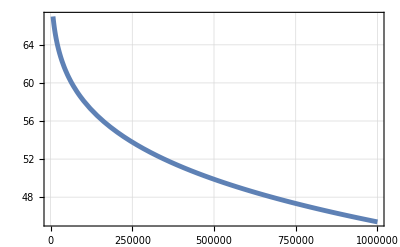

```mathematica
Plot[80-34.6*x^(1/5)/(10^6)^(1/5),{x,0,10^6}]
```

```mathematica
UnitSimplify[mhe*LinguisticAssistant/(ℏ*k0)]*10^6
```

61.4634 s

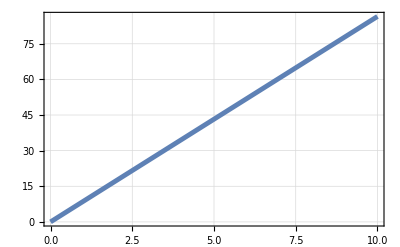

```mathematica
Plot[34.6*x/(4),{x,0,10}]
```